# Plotting Data

## Basic Exercises

### Question Subsection

Create the following sequences using the Table function.

evens={0,2,4,6,...,38,40}
odds={1,3,5,7,...,37,39}
primes={2,3,5,...,89,97}
fibonacci={1,1,2,3,...,610,987}

#### Hint

Even numbers can be produced using the formula 2n. 
Odd numbers can be produced using the formula 2n + 1.
Use the built-in function Prime[n_] along with Table for the third sequence. 
Use the built-in function Fibonacci[n_] along with Table for the fourth sequence.

#### Solution

```mathematica
evens=Table[2 n,{n,0,20}]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40}

```mathematica
odds=Table[2 n+1,{n,0,20}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41}

```mathematica
primes=Table[Prime[n],{n,1,25}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
fibo=Table[Fibonacci[n],{n,1,16}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987}

### Question Subsection

Produce pairwise values {x,y}, where x represents cos(t), y represents sin(t), and t ranges between 0 and 2π in increments of 0.1.

#### Solution

```mathematica
sincosdata=Table[{Cos[t],Sin[t]},{t,0,2 Pi,0.1}]
```

{{1.,0.},{0.995004,0.0998334},{0.980067,0.198669},{0.955336,0.29552},{0.921061,0.389418},{0.877583,0.479426},{0.825336,0.564642},{0.764842,0.644218},{0.696707,0.717356},{0.62161,0.783327},{0.540302,0.841471},{0.453596,0.891207},{0.362358,0.932039},{0.267499,0.963558},{0.169967,0.98545},{0.0707372,0.997495},{-0.0291995,0.999574},{-0.128844,0.991665},{-0.227202,0.973848},{-0.32329,0.9463},{-0.416147,0.909297},{-0.504846,0.863209},{-0.588501,0.808496},{-0.666276,0.745705},{-0.737394,0.675463},{-0.801144,0.598472},{-0.856889,0.515501},{-0.904072,0.42738},{-0.942222,0.334988},{-0.970958,0.239249},{-0.989992,0.14112},{-0.999135,0.0415807},{-0.998295,-0.0583741},{-0.98748,-0.157746},{-0.966798,-0.255541},{-0.936457,-0.350783},{-0.896758,-0.44252},{-0.8481,-0.529836},{-0.790968,-0.611858},{-0.725932,-0.687766},{-0.653644,-0.756802},{-0.574824,-0.818277},{-0.490261,-0.871576},{-0.400799,-0.916166},{-0.307333,-0.951602},{-0.210796,-0.97753},{-0.112153,-0.993691},{-0.0123887,-0.999923},{0.087499,-0.996165},{0.186512,-0.982453},{0.283662,-0.958924},{0.377978,-0.925815},{0.468517,-0.883455},{0.554374,-0.832267},{0.634693,-0.772764},{0.70867,-0.70554},{0.775566,-0.631267},{0.834713,-0.550686},{0.88552,-0.464602},{0.927478,-0.373877},{0.96017,-0.279415},{0.983268,-0.182163},{0.996542,-0.0830894}}

### Question Subsection

Plot the data you produced in the previous problem. Explore the options of the function ListPlot to make sure axes are scaled similarly. Jazz up the plot to your liking.

#### Solution

```mathematica
ListPlot[sincosdata,AspectRatio->1,Axes->False,PlotMarkers->"☺",PlotStyle->Magenta,Background->GrayLevel[.2]]
```

-Graphics-

### Question Subsection

Use table to generate pairwise data points for {x, x^2} for -3 < x < 3 with increments of 1. Plot these values using ListLinePlot

#### Solution

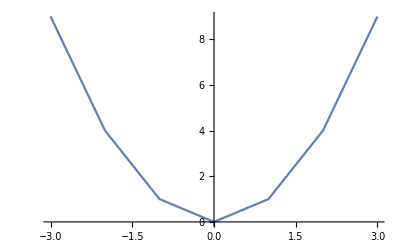

```mathematica
ListLinePlot[Table[{x,x^2},{x,-3,3}]]
```

### Question Subsection

In the exercise above, use the Option InterpolationOrder to plot the values for three different interpolation values of 0, 1, 2. Plot these in the same figure using Show.

#### Hint

You can use another Table function to produce different plots for each InterpolationOrder.

#### Solution

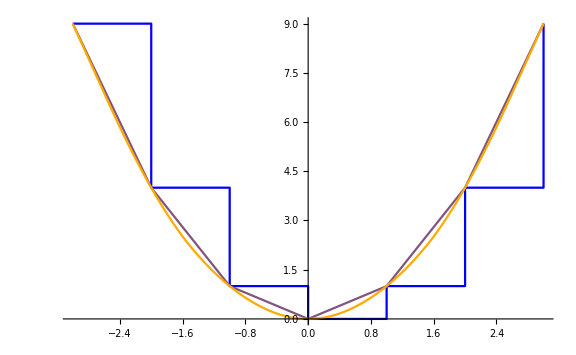

```mathematica
Show@Table[ListLinePlot[Table[{x,x^2},{x,-3,3}],InterpolationOrder->o,PlotStyle->RGBColor[o/2,o/3,(2-o)/2]],{o,{0,1,2}}]
```